```mathematica
table=Import["C:/Users/Gateway/Dropbox/School/RMath/GitHub/avgResults_gnm_4m_40n_20e.dat", "FieldSeparators"->"\t"];
```

```mathematica
results = table[[2;;]];
dataGcNNodes = {};
dataGcDiameter={};
dataNComponents={};
Do[
AppendTo[dataGcNNodes, result[[{1,2}]]];
AppendTo[dataGcDiameter, result[[{1,3}]]];
AppendTo[dataNComponents, result[[{1,4}]]];,
{result, results}];
```

```mathematica
iterTable=Import["C:/Users/Gateway/Dropbox/School/RMath/GitHub/iterResults_gnm_4m_40n_20e.dat", "FieldSeparators"->"\t"];
```

```mathematica
iterResults = iterTable[[2;;]];
iterDataGcNNodes = {};
iterDataGcDiameter={};
iterDataNComponents={};
Do[
AppendTo[iterDataGcNNodes, result[[{1,2}]]];
AppendTo[iterDataGcDiameter, result[[{1,3}]]];
AppendTo[iterDataNComponents, result[[{1,4}]]];,
{result, iterResults}];
```

## Used weighted_choice (times version) with 10 simulations

## Main Results

### Number of Nodes in Largest Component

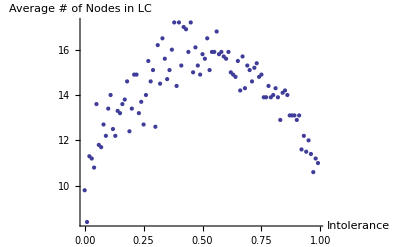

```mathematica
ListPlot[dataGcNNodes, AxesLabel->{"Intolerance", "Average # of Nodes in LC"}, PlotRange-> {Automatic, {0,Automatic}}]
```

### Diameter of Largest Component

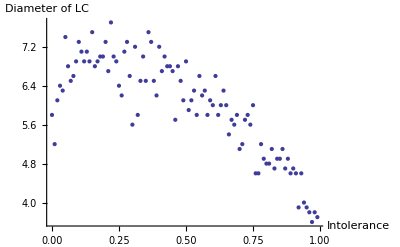

```mathematica
ListPlot[dataGcDiameter, AxesLabel->{"Intolerance", "Diameter of LC"}, PlotRange-> {Automatic, {0,Automatic}}]
```

### Number of Components

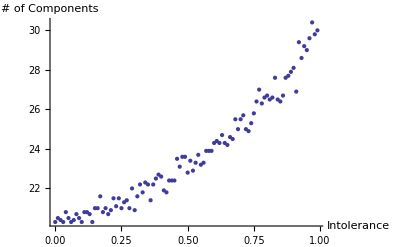

```mathematica
ListPlot[dataNComponents, AxesLabel->{"Intolerance", "# of Components"}, PlotRange-> {Automatic, {0,Automatic}}]
```

## Iter Results

### Number of Nodes in Giant Component

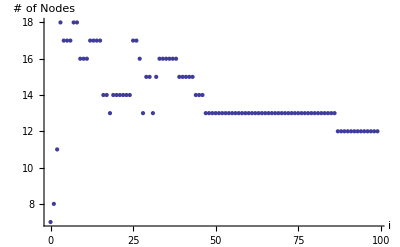

```mathematica
ListPlot[iterDataGcNNodes, AxesLabel->{i, "# of Nodes"}, PlotRange-> {Automatic, {0,Automatic}}]
```

### Diameter of Giant Component

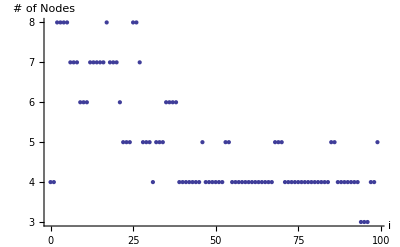

```mathematica
ListPlot[iterDataGcDiameter, AxesLabel->{i, "# of Nodes"}, PlotRange-> {Automatic, {0,Automatic}}]
```

### Number of Components

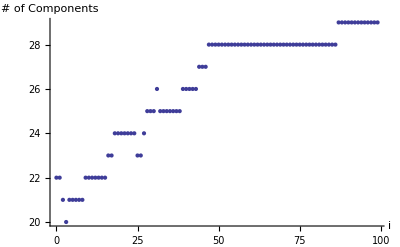

```mathematica
ListPlot[iterDataNComponents, AxesLabel->{i, "# of Components"}, PlotRange-> {Automatic, {0,Automatic}}]
```